# 38: Conjugate Gradients (CG)

We saw that Arnoldi and all sorts of other stuff became simpler for symmetric matrices. In particular, we could build a expanding orthogonal basis for the Krylov space  	
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b})
without orthogonalizing against all the previous directions.  The simplified process to build the tridiagonal H and the orthogonal Q was renamed the Lanczos process. Code to iteratively compute the diagonal α and subdiagonal β entries of H and the orthogonal Q is below.

```mathematica
LanczosInit[A_][q1_]:= Module[{v,α1,β1,q2},
v=A.q1;
α1=q1.v;
v = v - α1 q1;
β1=Norm[v];
q2=v/β1;
{{q1,q2}ᵀ,{{α1},{β1}}}
]
Lanczos[A_][{Q_,{α_,β_}}]:= Module[{m,n,qn,v,αn,βn,qNew},
{m,n}=Dimensions[Q];
qn=Q⟦All,n⟧;
v=A.qn;
αn=qn.v;
v=v-β⟦n-1⟧ Q⟦All,n-1⟧-αn qn;
βn=Norm[v];
qNew=v/βn;
{ArrayFlatten[({{Q, {qNew}ᵀ}})],{Append[α,αn],Append[β,βn]}}
]
```

Testing.  Note the preliminary initialization!

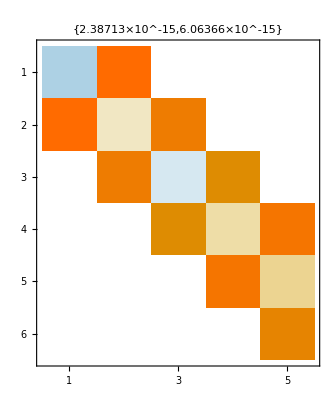

```mathematica
m=123;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
q1=Normalize[RandomReal[{-1,1},m]];
{Q1,{α1,β1}}=LanczosInit[A][q1];
n=5;
{Q,{α,β}}=Nest[Lanczos[A],{Q1,{α1,β1}},n-1];
H=SparseArray[{Band[{1,1}]->α,Band[{2,1}]->β,Band[{1,2}]->Drop[β,-1]}];
MatrixPlot[H,
PlotLabel->Map[Norm,{Qᵀ.Q-IdentityMatrix[n+1],A.Q⟦All,1;;n⟧-Q.H}]]
```

## Solving A.x=b with Conjugate Gradients.

From now on we are going to assume that A ϵ ℝ^(m×m) is Symmetric and Positive Definite abbreviated to SPD and write x_∞ for the solution satisfying A.x_∞=b.  As a reminder positive definite means x.A.x>0 unless x=0.  As a result SPD means ||x(||)_(CG(A)):=√(x.A.x) is a norm!   Minimizing the residual using this specially tailored norm makes the very simple and effective conjugate gradient algorithm.  The first thing to do is to work out what is special about this way of measuring the residual.  Take a look
  	||x-x_∞(||)_(CG(A))^2=(x-x_∞).A.(x-x_∞)=(x-x_∞).(A.x-A.x_∞)=(x-x_∞).(A.x-b)=x.A.x-x.b-x_∞.A.x+x_∞.b
  Maybe nothing stand out right now but remember A=Aᵀ so x_∞.A.x=(Aᵀ.x_∞).x=(A.x_∞).x=b.x so 
  	||x-x_∞(||)_(CG(A))^2=x.A.x-x.b-x_∞.A.x+x_∞.b=x.A.x-2 x.b+x_∞.b=2(1/2 x.A.x - b.x)+constant
  The original derivation defines
  	ϕ(x)=1/2 x.A.x - b.x
  and notes that the derivative
  	Dϕ(x)=A.x - b
  is readily computable.

This nor satisfies
	||x-x

We now have two different norms look at this norm of the error for a 2D test problem

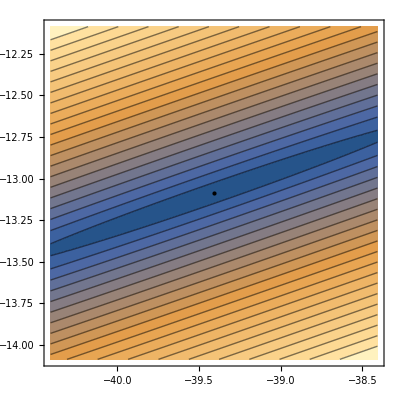

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
b=RandomReal[{-1,1},m];
{x1Mma,x2Mma}=LinearSolve[A,b];
CGNorm[A_][x_]:=√(x.A.x)
ContourPlot[CGNorm[A][{x1,x2}-{x1Mma,x2Mma}],
{x1,x1Mma-1,x1Mma+1},
{x2,x2Mma-1,x2Mma+1},
Contours->20,
Epilog->Point[{x1Mma,x2Mma}]
]
```

Algorithm 38.1 says x_n the current approximate solution, r_n a residual vector, and p_n a search direction should be initialized and updated as follows.

x_0=0, r_0=b, p_0=r_0
for n in 1, 2, 3, ...
	α_n=(r_(n-1).r_(n-1))/(p_(n-1).A.p_(n-1))
	x_n=x_n+α_n p_(n-1)
	r_n=r_(n-1)+α_n p_(n-1)
	β_n=(r_n.r_n)/(r_(n-1).r_(n-1))
	p_n=r_n+β_n p_(n-1)

The plan is to work out what this means and why it works. Apparently we always start our iteration at the origin!

We are go

(* Initialize 38.1 *)
	r0=b; p0=r0;x0=0*b;
	(* n=1 *)
	α1=(r0.r0)/(p0.A.p0);
	x1=x0+α1 p0;
	r1=r0-α1 A.p0;
	β1=(r1.r1)/(r0.r0);
	p1 = r1+ β1 p0;
	(* n=2 *)
	α2=(r1.r1)/(p1.A.p1);
	x2=x1+α2 p1;
	r2=r1-α2 A.p1;
	β2=(r2.r2)/(r1.r1);
	p2 = r2+ β2 p1;
	(* n=3 *) …
Conjugate Gradients always start at the origin so to make a picture we need to widen the picture to see the starting point.  the   Which could well be a long

The original derivation of CG that we are going to follow did not use the Krylov terminology. We are going to manually build out the computation in Algorithm 38.1 to see what properties it develops. As for Lanczos the initialization and first step i.e. n=1 is annoying because it refers to “0” entries.

```mathematica
m=12;
(* Create a random SPD test problem *)
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ;
b=RandomReal[{-1,1},m];
xMma =LinearSolve[A,b];
(* Initialize 38.1 *)
r0=b; p0=r0;x0=0*b;
(* n=1 *)
α1=(r0.r0)/(p0.A.p0);
x1=x0+α1 p0;
r1=r0-α1 A.p0;
β1=(r1.r1)/(r0.r0);
p1 = r1+ β1 p0;
(* n=2 *)
α2=(r1.r1)/(p1.A.p1);
x2=x1+α2 p1;
r2=r1-α2 A.p1;
β2=(r2.r2)/(r1.r1);
p2 = r2+ β2 p1;
(* n=3 - fill it in *)
```

xAll the operations for an iterative Krylov eigenvalue computation are faster for a Symmetric matrix:

The underlying Lanczos orthogonalization does not get slower as n grows. We can go longer without restarting.

Since eigenvalues and Ritz values are real there are only two big directions i.e. ±∞

The Ritz value computation is fast since the top square of H is symmetric tridiagonal.

### Easy Test

Lets see it work on a real matrix 
	https://math.nist.gov/MatrixMarket/data/Harwell-Boeing/bcsstruc1/bcsstk10.html

SparseArray[…]

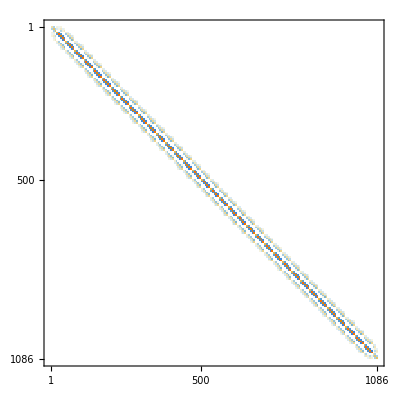

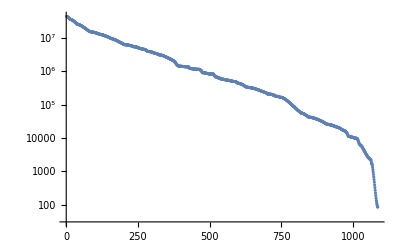

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk10.mtx.gz"]
MatrixPlot[A]
λs=Eigenvalues[Normal[A]];
ListLogPlot[λs]
```

We expect Lanczos to find the big eigenvalues and this is what the big ones look like!

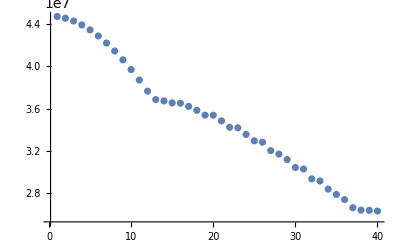

```mathematica
ListPlot[λs⟦1;;40⟧,
PlotRange->All]
```

Here is Lanczos

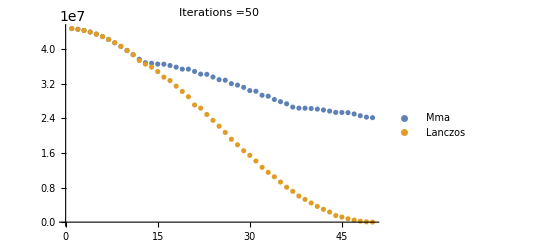

```mathematica
m=Length[A];
q1=Normalize[RandomReal[{-1,1},m]];
{Q1,{α1,β1}}=LanczosInit[A][q1];
n=50;
{Q,{α,β}}=Nest[Lanczos[A],{Q1,{α1,β1}},n-1];
H=SparseArray[{Band[{1,1}]->α,Band[{2,1}]->β,Band[{1,2}]->Drop[β,-1]}];
ListPlot[{
λs⟦1;;n⟧,
Eigenvalues[H⟦1;;n,1;;n⟧]
},
PlotLabel->StringForm["Iterations =``",n],
PlotLegends->{"Mma","Lanczos"}]
```

### Hard Test

Lets see it work on a hard real matrix 
	https://math.nist.gov/MatrixMarket/data/Harwell-Boeing/platz/plat1919.html

SparseArray[…]

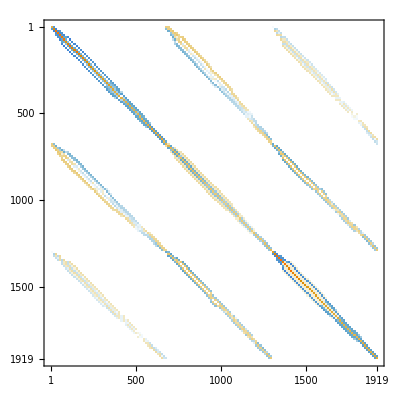

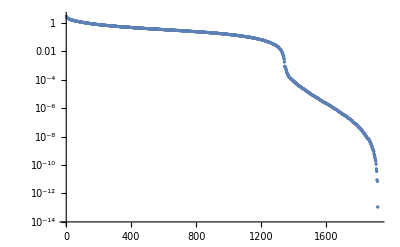

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/platz/plat1919.mtx.gz"]
MatrixPlot[A]
λs=Eigenvalues[Normal[A]];
ListLogPlot[λs]
```

We expect Lanczos to find the big eigenvalues and this is what the big ones look like!

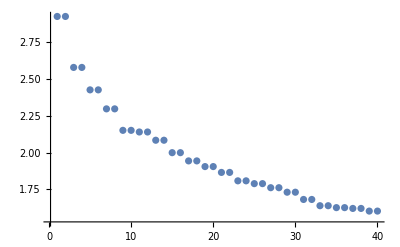

```mathematica
ListPlot[λs⟦1;;40⟧,
PlotRange->All]
```

This problem is in the test bank because these repeated eigenvalues make it hard for a simple Lanczos algorithm! It still finds eigenvalues but not always with the correct multiplicity!

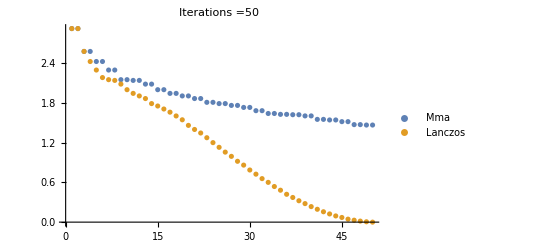

```mathematica
m=Length[A];
q1=Normalize[RandomReal[{-1,1},m]];
{Q1,{α1,β1}}=LanczosInit[A][q1];
n=50;
{Q,{α,β}}=Nest[Lanczos[A],{Q1,{α1,β1}},n-1];
H=SparseArray[{Band[{1,1}]->α,Band[{2,1}]->β,Band[{1,2}]->Drop[β,-1]}];
ListPlot[{
λs⟦1;;n⟧,
Eigenvalues[H⟦1;;n,1;;n⟧]
},
PlotLabel->StringForm["Iterations =``",n],
PlotLegends->{"Mma","Lanczos"}]
```

The Lanczos algorithm can miss duplicate eigenvalues.  Perhaps more disturbingly if you run it for a large number of steps it can find “ghost” eigenvalues that are extra copies!  The underlying problem is that the Q matrices can lose orthogonality. There are easy fixes! The easiest of all would be to use an Arnoldi solver that does a complete orthogonalization at every step rather than relying on the symmetry of A.

```mathematica
MatrixPlot[Qᵀ.Q,
PlotLegends->Automatic]
```

-Graphics-

## Bells and Whistles

Bells and whistles for Arnoldi include restarts and filters just like Arnoldi but now these include reorthogonalization and similar operations to accurately resolve eigenvalue multiplicity.